```mathematica
data1 = Import["lagrange1", "Table"];
data2 = Import["lagrange2", "Table"];
```

```mathematica
ll=ListLinePlot[{data1,data2},PlotStyle->{Red,Green}];
```

```mathematica
sin = Plot[1/(1+25x^2),{x,-1,1}];
```

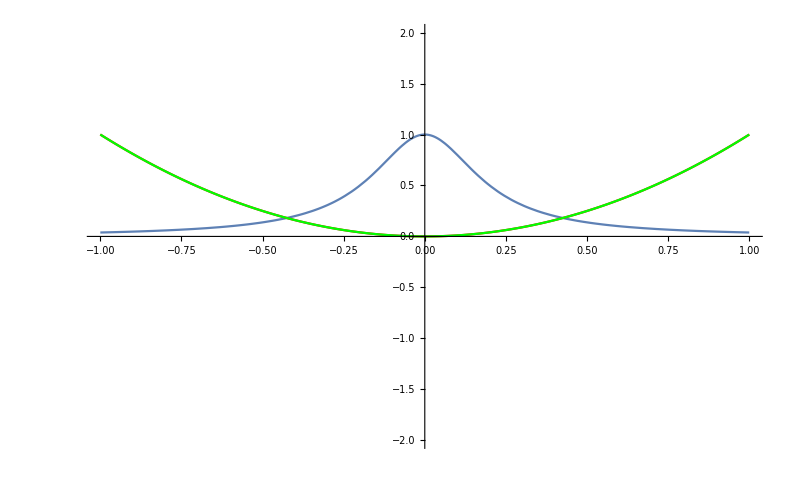

```mathematica
Show[sin,ll,PlotRange->{-2,2}]
```

```mathematica
splineData = Import["splineout", "Table"];
```

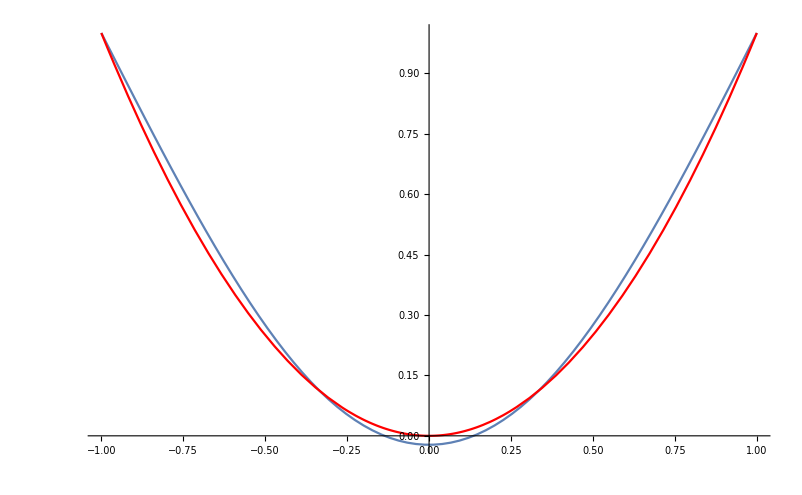

```mathematica
Show[ListLinePlot[splineData],Plot[x^2,{x,-1,1},PlotStyle->Red]]
```